```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=β[ω,δ,t,ϵ,m]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[m],Join[Table[{i,i-1},{i,Range[2,m,1]}],Table[{i,i+1},{i,Range[1,m,1]}]]->-t]
```

```mathematica
T[t_,m_]:=T[t,m]=t*IdentityMatrix[m]
```

```mathematica
Clear[LEFT]
```

```mathematica
leads=Table[ToExpression[Import["/home/shardulmukim/PhD/fwi/sq_lattice/50sq/leads/l"<>ToString[x]<>".dat"]],{x,Range[-2.5,2.5,0.01]}]
```

{1}
 |  |  |  |

```mathematica
LEFT[ω_,δ_,t_,ϵ_,m_]:=LEFT[ω,δ,t,ϵ,m]=leads[[Round[ω*100+251]]]
```

```mathematica
g[ω_,δ_,t_,ϵ_,m_]:= Inverse[β[ω,δ,t,ϵ,m]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-g[ω,δ,t,ϵ,m].T[t,m].LEFT[ω,δ,t,ϵ,m].T[t,m]].g[ω,δ,t,ϵ,m]
```

```mathematica
SL[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-g[ω,δ,t,ϵ,m].T[t,m].LEFT[ω,δ,t,ϵ,m].T[t,m]].g[ω,δ,t,ϵ,m]
```

```mathematica
IL[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-SL[ω,δ,t,ϵ,m].T[t,m].SR[ω,δ,t,ϵ,m].T[t,m]].SL[ω,δ,t,ϵ,m]
```

```mathematica
IR[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-SR[ω,δ,t,ϵ,m].T[t,m].SL[ω,δ,t,ϵ,m].T[t,m]].SR[ω,δ,t,ϵ,m]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_,m_]:= IL[ω,δ,t,ϵ,m]-ConjugateTranspose[IL[ω,δ,t,ϵ,m]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_,m_]:= IR[ω,δ,t,ϵ,m]-ConjugateTranspose[IR[ω,δ,t,ϵ,m]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_,m_]:= SR[ω,δ,t,ϵ,m].T[t,m].IL[ω,δ,t,ϵ,m]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_,m_]:= Gnonlocal[ω,δ,t,ϵ,m]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ,m]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_,m_]:= Abs[Tr[gdd[ω,δ,t,ϵ,m].T[t,m].grr[ω,δ,t,ϵ,m].T[t,m]-T[t,m].GNON[ω,δ,t,ϵ,m].T[t,m].GNON[ω,δ,t,ϵ,m]]]
```

```mathematica
pris=Compile[{ω},tr[ω,0.0001,5,0,100],CompilationTarget->"C",Parallelization->True]
```

CompiledFunction[…]

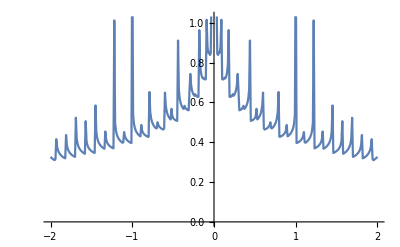

```mathematica
ListLinePlot[Table[{ω,-Im[IL[ω,0.0001,1,0,50][[25,25]]]},{ω,Range[-2,2,0.01]}]]
```

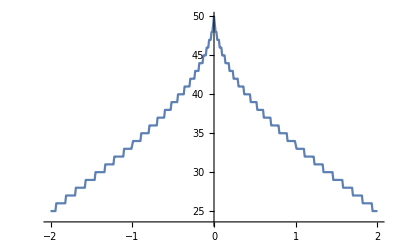

```mathematica
ListLinePlot[Table[{ω,tr[ω,0.0001,1,0,50]},{ω,Range[-2,2,0.01]}]]
```

```mathematica
Clear[LEFT,β,T,g,SR,SL,IL,IR,gdd,grr,Gnonlocal]
```

```mathematica
β1[ω_,δ_,t_,ϵ_,m_]:=β1[ω,δ,t,ϵ,m]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[m],Join[Table[{i,i-1},{i,Range[2,m,1]}],Table[{i,i+1},{i,Range[1,m,1]}]]->-t]
```

```mathematica
T1[t_,m_]:=T1[t,m]=t*IdentityMatrix[m]
```

```mathematica
Clear[LEFT1]
```

```mathematica
leads1=Table[ToExpression[Import["/home/shardulmukim/PhD/fwi/sq_lattice/10sq/leads/lead_"<>ToString[x]<>".dat"]],{x,Range[-2.5,2.5,0.01]}]
```

{1}
 |  |  |  |

```mathematica
LEFT1[ω_,δ_,t_,ϵ_,m_]:=LEFT1[ω,δ,t,ϵ,m]= leads1[[Round[ω*100+251]]]
```

```mathematica
LEFT1[0,0.0001,1,0,10]//MatrixForm//AbsoluteTiming
```

{0.00002,(0.-0.848848 ⅈ | -0.499958+0. ⅈ | 0.+0.169538 ⅈ | 0.0000151947+0. ⅈ | 0.+0.0238287 ⅈ | 8.17142×10^-6+0. ⅈ | 0.+0.00738028 ⅈ | 4.25185×10^-6+0. ⅈ | 0.+0.00251854 ⅈ | 1.33811×10^-6+0. ⅈ
-0.499958+0. ⅈ | 0.-0.679311 ⅈ | -0.499943+0. ⅈ | 0.+0.193366 ⅈ | 0.0000233662+0. ⅈ | 0.+0.031209 ⅈ | 0.0000124233+0. ⅈ | 0.+0.00989882 ⅈ | 5.58996×10^-6+0. ⅈ | 0.+0.00251854 ⅈ
0.+0.169538 ⅈ | -0.499943+0. ⅈ | 0.-0.655482 ⅈ | -0.499935+0. ⅈ | 0.+0.200747 ⅈ | 0.000027618+0. ⅈ | 0.+0.0337276 ⅈ | 0.0000137614+0. ⅈ | 0.+0.00989882 ⅈ | 4.25185×10^-6+0. ⅈ
0.0000151947+0. ⅈ | 0.+0.193366 ⅈ | -0.499935+0. ⅈ | 0.-0.648102 ⅈ | -0.499931+0. ⅈ | 0.+0.203265 ⅈ | 0.0000289561+0. ⅈ | 0.+0.0337276 ⅈ | 0.0000124233+0. ⅈ | 0.+0.00738028 ⅈ
0.+0.0238287 ⅈ | 0.0000233662+0. ⅈ | 0.+0.200747 ⅈ | -0.499931+0. ⅈ | 0.-0.645583 ⅈ | -0.499929+0. ⅈ | 0.+0.203265 ⅈ | 0.000027618+0. ⅈ | 0.+0.031209 ⅈ | 8.17142×10^-6+0. ⅈ
8.17142×10^-6+0. ⅈ | 0.+0.031209 ⅈ | 0.000027618+0. ⅈ | 0.+0.203265 ⅈ | -0.499929+0. ⅈ | 0.-0.645583 ⅈ | -0.499931+0. ⅈ | 0.+0.200747 ⅈ | 0.0000233662+0. ⅈ | 0.+0.0238287 ⅈ
0.+0.00738028 ⅈ | 0.0000124233+0. ⅈ | 0.+0.0337276 ⅈ | 0.0000289561+0. ⅈ | 0.+0.203265 ⅈ | -0.499931+0. ⅈ | 0.-0.648102 ⅈ | -0.499935+0. ⅈ | 0.+0.193366 ⅈ | 0.0000151947+0. ⅈ
4.25185×10^-6+0. ⅈ | 0.+0.00989882 ⅈ | 0.0000137614+0. ⅈ | 0.+0.0337276 ⅈ | 0.000027618+0. ⅈ | 0.+0.200747 ⅈ | -0.499935+0. ⅈ | 0.-0.655482 ⅈ | -0.499943+0. ⅈ | 0.+0.169538 ⅈ
0.+0.00251854 ⅈ | 5.58996×10^-6+0. ⅈ | 0.+0.00989882 ⅈ | 0.0000124233+0. ⅈ | 0.+0.031209 ⅈ | 0.0000233662+0. ⅈ | 0.+0.193366 ⅈ | -0.499943+0. ⅈ | 0.-0.679311 ⅈ | -0.499958+0. ⅈ
1.33811×10^-6+0. ⅈ | 0.+0.00251854 ⅈ | 4.25185×10^-6+0. ⅈ | 0.+0.00738028 ⅈ | 8.17142×10^-6+0. ⅈ | 0.+0.0238287 ⅈ | 0.0000151947+0. ⅈ | 0.+0.169538 ⅈ | -0.499958+0. ⅈ | 0.-0.848848 ⅈ)}

```mathematica
Diagonal[LEFT1[0,0.0001,1,0,10]]//Reverse
```

{0.-0.848848 ⅈ,0.-0.679311 ⅈ,0.-0.655482 ⅈ,0.-0.648102 ⅈ,0.-0.645583 ⅈ,0.-0.645583 ⅈ,0.-0.648102 ⅈ,0.-0.655482 ⅈ,0.-0.679311 ⅈ,0.-0.848848 ⅈ}

```mathematica
g1[ω_,δ_,t_,ϵ_,m_]:= Inverse[β1[ω,δ,t,ϵ,m]]
```

```mathematica
SR1[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-g1[ω,δ,t,ϵ,m].T1[t,m].LEFT1[ω,δ,t,ϵ,m].T1[t,m]].g1[ω,δ,t,ϵ,m]
```

```mathematica
SL1[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-g1[ω,δ,t,ϵ,m].T1[t,m].LEFT1[ω,δ,t,ϵ,m].T1[t,m]].g1[ω,δ,t,ϵ,m]
```

```mathematica
IL1[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-SL1[ω,δ,t,ϵ,m].T1[t,m].SR1[ω,δ,t,ϵ,m].T1[t,m]].SL1[ω,δ,t,ϵ,m]
```

```mathematica
IR1[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-SR1[ω,δ,t,ϵ,m].T1[t,m].SL1[ω,δ,t,ϵ,m].T1[t,m]].SR1[ω,δ,t,ϵ,m]
```

```mathematica
gdd1[ω_,δ_,t_,ϵ_,m_]:= IL1[ω,δ,t,ϵ,m]-ConjugateTranspose[IL1[ω,δ,t,ϵ,m]]
```

```mathematica
grr1[ω_,δ_,t_,ϵ_,m_]:= IR1[ω,δ,t,ϵ,m]-ConjugateTranspose[IR1[ω,δ,t,ϵ,m]]
```

```mathematica
Gnonlocal1[ω_,δ_,t_,ϵ_,m_]:= SR1[ω,δ,t,ϵ,m].T1[t,m].IL1[ω,δ,t,ϵ,m]
```

```mathematica
GNON1[ω_,δ_,t_,ϵ_,m_]:= Gnonlocal1[ω,δ,t,ϵ,m]-ConjugateTranspose[Gnonlocal1[ω,δ,t,ϵ,m]]
```

```mathematica
tr1[ω_,δ_,t_,ϵ_,m_]:= Abs[Tr[gdd1[ω,δ,t,ϵ,m].T1[t,m].grr1[ω,δ,t,ϵ,m].T1[t,m]-T1[t,m].GNON1[ω,δ,t,ϵ,m].T1[t,m].GNON1[ω,δ,t,ϵ,m]]]
```

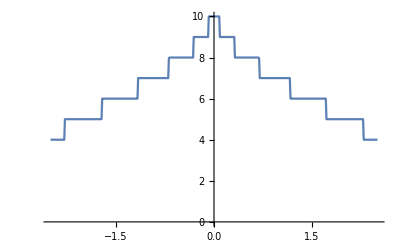

```mathematica
ListLinePlot[Table[{ω,tr1[ω,0.0001,1,0,10]},{ω,Range[-2.5,2.5,0.01]}]]
```

```mathematica
Clear[unit]
```

```mathematica
F[n_]:= {n,n}
```

```mathematica
unit[ω_,δ_,t_,ϵ_,ϵ1_,n_]:=Module[{b=β[ω,δ,t,ϵ,50]},ReplacePart[b,Table[F[RandomSample[{RandomInteger[{2,49}]},1]]//Flatten,n]->ω+ⅈ*δ-ϵ1]]
```

```mathematica
device[ω_,δ_,t_,ϵ_,ϵ1_,m_,num1_,num2_,n1_,n2_]:=Module[{Tin=T[1,m],list,b2},
list={RandomSample[Join[Table[unit[ω,0.0001,1,0,ϵ1,n1],num1],Table[unit[ω,0.0001,1,0,ϵ1,n2],num2] ,Table[unit[ω,0.0001,1,0,0,1],50-num2-num1]]]};
sl1= Module[{J=SL[ω,0.0001,1,0,m]},Do[J=Inverse[IdentityMatrix[m]-Inverse[ReplacePart[list[[1,ζ]],{{1,1},{50,50}}->ω+ⅈ*δ-t*t*LEFT[ω,δ,t,ϵ,50][[ζ,ζ]]]].ConjugateTranspose[Tin].J.Tin].Inverse[ReplacePart[list[[1,ζ]],{{1,1},{50,50}}->ω+ⅈ*δ-t*t*LEFT[ω,δ,t,ϵ,50][[ζ,ζ]]]],{ζ,1,50}];
 J=J];
Il1:=Inverse[IdentityMatrix[m]-sl1.Tin.SL[ω,0.0001,1,0,m].Tin].sl1;
Ir1:=Inverse[IdentityMatrix[m]-SL[ω,0.0001,1,0,m].Tin.sl1.Tin].SL[ω,0.0001,1,0,m];gdd1:=Il1-ConjugateTranspose[Il1];grr1:=Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SL[ω,0.0001,1,0,m].Tin.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.Tin.grr1.Tin-Tin.GNON1.Tin.GNON1]]>tr[ω,0.0001,1,0,m],tr[ω,0.0001,1,0,m],Abs[Tr[gdd1.Tin.grr1.Tin-Tin.GNON1.Tin.GNON1]]]]
```

```mathematica
Table[Print["Concentration ================================================= is " <>ToString[150+2*num]<>"."];Export["/home/shardulmukim/PhD/fwi/sq_lattice/50sq/CA_"<>ToString[150+2*num]<>".dat",Table[{ω,Print["WOrking on"<>ToString[ω]<>"!!!!"];Mean[ParallelTable[device[ω,0.0001,1,0,0.5,50,25,num,6,2],2500]]},{ω,Range[-0.5,0.5,0.01]}]],{num,Range[5,25,5]}]
```

{/home/shardulmukim/PhD/fwi/sq_lattice/50sq/CA_160.dat,/home/shardulmukim/PhD/fwi/sq_lattice/50sq/CA_170.dat,/home/shardulmukim/PhD/fwi/sq_lattice/50sq/CA_180.dat,/home/shardulmukim/PhD/fwi/sq_lattice/50sq/CA_190.dat,/home/shardulmukim/PhD/fwi/sq_lattice/50sq/CA_200.dat}

```mathematica
Range[5,25,5]
```

{5,10,15,20,25}

```mathematica
Table[Print["Concentration ================================================= is " <>ToString[2*num]<>"."];Export["/home/shardulmukim/PhD/fwi/sq_lattice/50sq/CA_10_sec_"<>ToString[2*num]<>".dat",Table[{ω,Print["Working on"<>ToString[ω]<>"!!!!"];Mean[ParallelTable[device[ω,0.0001,1,0,0.5,50,num,2],2500]]},{ω,Range[-0.5,0.5,0.01]}]],{num,Range[5,10,1]}]
```

{/home/shardulmukim/PhD/fwi/sq_lattice/50sq/CA_10_sec_10.dat,/home/shardulmukim/PhD/fwi/sq_lattice/50sq/CA_10_sec_12.dat,/home/shardulmukim/PhD/fwi/sq_lattice/50sq/CA_10_sec_14.dat,/home/shardulmukim/PhD/fwi/sq_lattice/50sq/CA_10_sec_16.dat,/home/shardulmukim/PhD/fwi/sq_lattice/50sq/CA_10_sec_18.dat,/home/shardulmukim/PhD/fwi/sq_lattice/50sq/CA_10_sec_20.dat}

```mathematica
LaunchKernels[4]
```

{KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…]}

```mathematica
Table[Print["Concentration ================================================= is " <>ToString[num]<>"."];Export["/home/shardulmukim/PhD/fwi/sq_lattice/50sq/CA_"<>ToString[2*num]<>".dat",Table[{ω,Print["WOrking on"<>ToString[ω]<>"!!!!"];Mean[ParallelTable[device[ω,0.0001,1,0,0.5,50,num,3],2500]]},{ω,Range[-0.5,0.5,0.01]}]],{num,Range[30,40,5]}]
```

```mathematica
Export["/home/shardulmukim/PhD/fwi/sq_lattice/50sq/CA_"<>ToString[100]<>".dat",Table[{ω,Print["WOrking on"<>ToString[ω]<>"!!!!"];Mean[ParallelTable[device[ω,0.0001,1,0,0.5,50,25,4],2500]]},{ω,Range[-0.5,0.5,0.01]}]]
```

/home/shardulmukim/PhD/fwi/sq_lattice/50sq/CA_100.dat

```mathematica
Export["/home/shardulmukim/PhD/fwi/sq_lattice/50sq/CA_"<>ToString[90]<>".dat",Table[{ω,Print["WOrking on"<>ToString[ω]<>"!!!!"];Mean[ParallelTable[device[ω,0.0001,1,0,0.5,50,30,3],2500]]},{ω,Range[-0.5,0.5,0.01]}]]
```

/home/shardulmukim/PhD/fwi/sq_lattice/50sq/CA_90.dat

```mathematica
device10[ω_,δ_,t_,ϵ_,ϵ1_,m_,num_,n_]:=Module[{Tin=T[1,m],list,b2},
list={RandomSample[Join[Table[unit[ω,0.0001,1,0,ϵ1,n],num],Table[unit[ω,0.0001,1,0,0,1],10-num]]]};
sl1= Module[{J=SL[ω,0.0001,1,0,m]},Do[J=Inverse[IdentityMatrix[m]-Inverse[ReplacePart[list[[1,ζ]],{{1,1},{50,50}}->ω+ⅈ*δ-t*t*LEFT[ω,δ,t,ϵ,50][[ζ,ζ]]]].ConjugateTranspose[Tin].J.Tin].Inverse[ReplacePart[list[[1,ζ]],{{1,1},{50,50}}->ω+ⅈ*δ-t*t*LEFT[ω,δ,t,ϵ,50][[ζ,ζ]]]],{ζ,1,50}];
 J=J];
Il1:=Inverse[IdentityMatrix[m]-sl1.Tin.SL[ω,0.0001,1,0,m].Tin].sl1;
Ir1:=Inverse[IdentityMatrix[m]-SL[ω,0.0001,1,0,m].Tin.sl1.Tin].SL[ω,0.0001,1,0,m];gdd1:=Il1-ConjugateTranspose[Il1];grr1:=Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SL[ω,0.0001,1,0,m].Tin.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.Tin.grr1.Tin-Tin.GNON1.Tin.GNON1]]>tr[ω,0.0001,1,0,m],tr[ω,0.0001,1,0,m],Abs[Tr[gdd1.Tin.grr1.Tin-Tin.GNON1.Tin.GNON1]]]]
```

```mathematica
Table[Print["Concentration ================================================= is " <>ToString[num]<>"."];Export["/home/shardulmukim/PhD/fwi/sq_lattice/50sq/CA_"<>ToString[2*num]<>".dat",Table[{ω,Print["WOrking on"<>ToString[ω]<>"!!!!"];Mean[ParallelTable[device[ω,0.0001,1,0,0.5,50,num,2],2500]]},{ω,Range[-0.5,0.5,0.01]}]],{num,Range[10,40,5]}]
```

```mathematica
Range[5,40,5]
```

{5,10,15,20,25,30,35,40}

```mathematica
Table[{ω,Print["WOrking on"<>ToString[ω]<>"!!!!"];Mean[ParallelTable[device[ω,0.5,50],2500]]},{ω,Range[-0.5,0.5,0.01]}]
```

{{-0.5,37.583},{-0.49,37.684},{-0.48,37.7226},{-0.47,37.7138},{-0.46,37.6222},{-0.45,37.2305},{-0.44,37.1655},{-0.43,38.1953},{-0.42,38.4197},{-0.41,38.5278},{-0.4,38.562},{-0.39,38.5255},{-0.38,38.3236},{-0.37,36.9528},{-0.36,38.7217},{-0.35,39.1435},{-0.34,39.292},{-0.33,39.3512},{-0.32,39.3074},{-0.31,39.039},{-0.3,35.8687},{-0.29,39.5263},{-0.28,39.9149},{-0.27,40.0473},{-0.26,40.0591},{-0.25,39.8606},{-0.24,38.0095},{-0.23,39.969},{-0.22,40.5094},{-0.21,40.6742},{-0.2,40.6479},{-0.19,40.1073},{-0.18,39.2425},{-0.17,40.7768},{-0.16,41.1083},{-0.15,41.0735},{-0.14,40.2112},{-0.13,39.9031},{-0.12,41.1082},{-0.11,41.2953},{-0.1,40.5755},{-0.09,39.1549},{-0.08,40.866},{-0.07,40.8064},{-0.06,31.9286},{-0.05,39.5679},{-0.04,39.066},{-0.03,35.0616},{-0.02,35.7283},{-0.01,29.2285},{0.,19.6615},{0.01,15.7945},{0.02,14.1537},{0.03,31.1994},{0.04,21.583},{0.05,36.2708},{0.06,31.041},{0.07,34.0998},{0.08,38.6196},{0.09,38.0209},{0.1,28.5098},{0.11,38.6567},{0.12,39.6659},{0.13,39.0249},{0.14,28.6554},{0.15,38.5785},{0.16,39.7245},{0.17,39.788},{0.18,38.7207},{0.19,33.6633},{0.2,38.695},{0.21,39.499},{0.22,39.6264},{0.23,39.2598},{0.24,33.3913},{0.25,37.0699},{0.26,38.7828},{0.27,39.1524},{0.28,39.1659},{0.29,38.9128},{0.3,35.918},{0.31,36.1565},{0.32,38.0753},{0.33,38.5231},{0.34,38.6155},{0.35,38.5309},{0.36,38.1964},{0.37,35.1038},{0.38,36.3364},{0.39,37.5155},{0.4,37.8455},{0.41,37.9289},{0.42,37.8852},{0.43,37.6944},{0.44,36.9056},{0.45,35.0646},{0.46,36.4604},{0.47,36.9804},{0.48,37.1436},{0.49,37.1734},{0.5,37.1161}}

```mathematica
device2[ω_,ϵ1_,m_]:=Module[{Tin=T[1,m],list,b2},
(*b2=Module[{},*)list={{unitcell2[ω,0.0001,1,0,ϵ1,1],unitcell2[ω,0.0001,1,0,ϵ1,2],unitcell2[ω,0.0001,1,0,ϵ1,3],unitcell2[ω,0.0001,1,0,ϵ1,4],unitcell2[ω,0.0001,1,0,ϵ1,5],unitcell2[ω,0.0001,1,0,ϵ1,6],unitcell2[ω,0.0001,1,0,ϵ1,7],unitcell2[ω,0.0001,1,0,ϵ1,8],unitcell2[ω,0.0001,1,0,ϵ1,9],unitcell2[ω,0.0001,1,0,ϵ1,10]}};
sl1= Module[{J=SL[ω,0.0001,1,0,m]},Do[J=Inverse[IdentityMatrix[m]-list[[1,ζ]].ConjugateTranspose[Tin].J.Tin].list[[1,ζ]],{ζ,1,10}];
 J=J];
Il1:=Inverse[IdentityMatrix[m]-sl1.Tin.SL[ω,0.0001,1,0,m].Tin].sl1;
Ir1:=Inverse[IdentityMatrix[m]-SL[ω,0.0001,1,0,m].Tin.sl1.Tin].SL[ω,0.0001,1,0,m];gdd1:=Il1-ConjugateTranspose[Il1];grr1:=Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SL[ω,0.0001,1,0,m].Tin.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.Tin.grr1.Tin-Tin.GNON1.Tin.GNON1]]>tr[ω,0.0001,1,0,m],tr[ω,0.0001,1,0,m],Abs[Tr[gdd1.Tin.grr1.Tin-Tin.GNON1.Tin.GNON1]]]](*;
b2]*)
```

```mathematica
Table[{ω,Print["WOrking on"<>ToString[ω]<>"!!!!"];Mean[ParallelTable[device2[ω,0.5,50],2500]]},{ω,Range[-0.5,0.5,0.01]}]
```

{{-0.5,36.6036},{-0.49,36.7529},{-0.48,36.8411},{-0.47,36.8589},{-0.46,36.767},{-0.45,36.3985},{-0.44,35.7016},{-0.43,36.9208},{-0.42,37.2772},{-0.41,37.4548},{-0.4,37.5299},{-0.39,37.5188},{-0.38,37.3269},{-0.37,36.1846},{-0.36,37.1498},{-0.35,37.7359},{-0.34,37.9935},{-0.33,38.1119},{-0.32,38.1087},{-0.31,37.8564},{-0.3,35.4027},{-0.29,37.7299},{-0.28,38.286},{-0.27,38.5193},{-0.26,38.5918},{-0.25,38.4095},{-0.24,36.9723},{-0.23,37.8287},{-0.22,38.5404},{-0.21,38.8207},{-0.2,38.8416},{-0.19,38.3596},{-0.18,36.8413},{-0.17,38.3192},{-0.16,38.7633},{-0.15,38.7899},{-0.14,38.0155},{-0.13,36.8943},{-0.12,38.078},{-0.11,38.3422},{-0.1,37.6566},{-0.09,35.4973},{-0.08,36.9106},{-0.07,36.844},{-0.06,31.0067},{-0.05,34.4301},{-0.04,33.7825},{-0.03,29.5134},{-0.02,28.9156},{-0.01,22.2556},{0.,15.9537},{0.01,31.5311},{0.02,28.016},{0.03,15.5891},{0.04,9.75679},{0.05,22.9196},{0.06,26.1448},{0.07,15.3655},{0.08,30.2937},{0.09,32.4214},{0.1,17.902},{0.11,29.9371},{0.12,34.4969},{0.13,34.903},{0.14,25.0444},{0.15,30.7599},{0.16,35.3946},{0.17,36.2726},{0.18,35.5968},{0.19,28.1484},{0.2,33.0104},{0.21,36.0078},{0.22,36.7186},{0.23,36.5838},{0.24,33.2591},{0.25,31.3121},{0.26,35.146},{0.27,36.5061},{0.28,36.8612},{0.29,36.6831},{0.3,34.6054},{0.31,31.9154},{0.32,34.6906},{0.33,36.1612},{0.34,36.6105},{0.35,36.6318},{0.36,36.324},{0.37,34.1557},{0.38,32.9569},{0.39,34.8472},{0.4,35.8834},{0.41,36.2275},{0.42,36.2727},{0.43,36.0807},{0.44,35.2724},{0.45,33.2929},{0.46,33.8694},{0.47,35.0705},{0.48,35.5924},{0.49,35.7581},{0.5,35.7518}}

```mathematica
device3[ω_,ϵ1_,m_]:=Module[{Tin=T[1,m],list,b2},
(*b2=Module[{},*)list={{unitcell3[ω,0.0001,1,0,ϵ1,1],unitcell3[ω,0.0001,1,0,ϵ1,2],unitcell3[ω,0.0001,1,0,ϵ1,3],unitcell3[ω,0.0001,1,0,ϵ1,4],unitcell3[ω,0.0001,1,0,ϵ1,5],unitcell3[ω,0.0001,1,0,ϵ1,6],unitcell3[ω,0.0001,1,0,ϵ1,7],unitcell3[ω,0.0001,1,0,ϵ1,8],unitcell3[ω,0.0001,1,0,ϵ1,9],unitcell3[ω,0.0001,1,0,ϵ1,10]}};
sl1= Module[{J=SL[ω,0.0001,1,0,m]},Do[J=Inverse[IdentityMatrix[m]-list[[1,ζ]].ConjugateTranspose[Tin].J.Tin].list[[1,ζ]],{ζ,1,10}];
 J=J];
Il1:=Inverse[IdentityMatrix[m]-sl1.Tin.SL[ω,0.0001,1,0,m].Tin].sl1;
Ir1:=Inverse[IdentityMatrix[m]-SL[ω,0.0001,1,0,m].Tin.sl1.Tin].SL[ω,0.0001,1,0,m];gdd1:=Il1-ConjugateTranspose[Il1];grr1:=Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SL[ω,0.0001,1,0,m].Tin.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.Tin.grr1.Tin-Tin.GNON1.Tin.GNON1]]>tr[ω,0.0001,1,0,m],tr[ω,0.0001,1,0,m],Abs[Tr[gdd1.Tin.grr1.Tin-Tin.GNON1.Tin.GNON1]]]](*;
b2]*)
```

```mathematica
Table[{ω,Print["WOrking on"<>ToString[ω]<>"!!!!"];Mean[ParallelTable[device3[ω,0.5,50],2500]]},{ω,Range[-0.5,0.5,0.01]}]
```

{{-0.5,35.6604},{-0.49,35.8615},{-0.48,35.9807},{-0.47,36.0256},{-0.46,35.9643},{-0.45,35.6604},{-0.44,34.7519},{-0.43,35.806},{-0.42,36.2031},{-0.41,36.4063},{-0.4,36.5324},{-0.39,36.5482},{-0.38,36.4003},{-0.37,35.5407},{-0.36,35.9017},{-0.35,36.4798},{-0.34,36.7775},{-0.33,36.9303},{-0.32,36.9473},{-0.31,36.7622},{-0.3,35.0632},{-0.29,36.3201},{-0.28,36.8329},{-0.27,37.1068},{-0.26,37.2103},{-0.25,37.0789},{-0.24,36.0246},{-0.23,36.2569},{-0.22,36.8478},{-0.21,37.1277},{-0.2,37.1973},{-0.19,36.7997},{-0.18,35.3331},{-0.17,36.3461},{-0.16,36.7239},{-0.15,36.775},{-0.14,36.1319},{-0.13,34.9148},{-0.12,35.6599},{-0.11,35.825},{-0.1,35.2178},{-0.09,33.3253},{-0.08,33.9989},{-0.07,33.699},{-0.06,29.5279},{-0.05,30.9027},{-0.04,29.8938},{-0.03,25.9448},{-0.02,24.6057},{-0.01,19.0389},{0.,13.7938},{0.01,20.1604},{0.02,19.274},{0.03,9.82162},{0.04,8.5596},{0.05,8.72475},{0.06,18.3419},{0.07,10.4199},{0.08,19.0972},{0.09,25.865},{0.1,21.5698},{0.11,20.1966},{0.12,28.0538},{0.13,30.38},{0.14,26.9781},{0.15,23.9754},{0.16,29.6132},{0.17,32.3339},{0.18,32.4346},{0.19,29.0056},{0.2,27.5576},{0.21,31.6555},{0.22,33.5667},{0.23,33.91},{0.24,32.218},{0.25,29.4037},{0.26,30.8248},{0.27,33.3722},{0.28,34.3542},{0.29,34.4465},{0.3,33.0189},{0.31,31.1293},{0.32,31.163},{0.33,33.3385},{0.34,34.424},{0.35,34.7494},{0.36,34.5003},{0.37,33.1475},{0.38,31.7384},{0.39,32.0793},{0.4,33.5772},{0.41,34.4026},{0.42,34.665},{0.43,34.5488},{0.44,33.7082},{0.45,32.6747},{0.46,31.9847},{0.47,32.8867},{0.48,33.8341},{0.49,34.2805},{0.5,34.3824}}

```mathematica
30/500
```

3/50

```mathematica
N[4/50]
```

0.08

```mathematica
%117[[51]]
```

{0.,19.6615}

```mathematica
υnew[n_,num_,x_,y_]:=Module[{m5=ParallelTable[{ω,device2[ω,0.5,50]},{ω,Range[-0.5,0.5,0.01]}]},
ρ1:=Module[{B1=Transpose[{m5[[1;;101]][[;;,1]],(m5[[1;;101,2]]-%117[[1;;101,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ2:=Module[{B1=Transpose[{m5[[1;;101]][[;;,1]],(m5[[1;;101,2]]-%122[[1;;101,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ3:=Module[{B1=Transpose[{m5[[1;;101]][[;;,1]],(m5[[1;;101,2]]-%123[[1;;101,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];
{ρ1,ρ2,ρ3}]
```

```mathematica
Table[υnew[0,0,0.5,-0.5],100]
```

{{0.395823,0.070655,0.229864},{0.351625,0.0706098,0.179824},{0.385964,0.0722842,0.284842},{0.478945,0.10907,0.337032},{0.353988,0.0582515,0.202982},{0.362642,0.0841845,0.236212},{0.422145,0.0999732,0.208709},{0.406724,0.0682628,0.202121},{0.233881,0.110113,0.194833},{0.348992,0.0745886,0.161928},{0.402775,0.062601,0.21762},{0.251248,0.142153,0.205413},{0.388702,0.0792466,0.292428},{0.301654,0.154299,0.217134},{0.37716,0.0675906,0.249592},{0.280611,0.124004,0.174309},{0.423591,0.0867628,0.253708},{0.313371,0.0395899,0.198405},{0.373966,0.0690461,0.277705},{0.248907,0.103721,0.20938},{0.235208,0.174434,0.227107},{0.404385,0.128177,0.28083},{0.298711,0.0994917,0.226572},{0.302624,0.10225,0.305873},{0.396914,0.106042,0.29966},{0.223982,0.142257,0.213739},{0.324537,0.0647138,0.245872},{0.350914,0.0768415,0.160997},{0.243939,0.106747,0.188029},{0.337454,0.132028,0.324437},{0.184685,0.125804,0.211008},{0.353855,0.103975,0.227365},{0.404166,0.0880671,0.277978},{0.28274,0.0737085,0.261452},{0.442386,0.0887138,0.220232},{0.377041,0.0638014,0.163259},{0.479269,0.122216,0.321473},{0.454307,0.0947155,0.210441},{0.238835,0.0741205,0.158484},{0.392449,0.194323,0.322646},{0.251383,0.0531051,0.1637},{0.284702,0.151779,0.223029},{0.31247,0.0891702,0.176048},{0.547285,0.153195,0.245311},{0.346768,0.0846734,0.310901},{0.348051,0.109599,0.258137},{0.422672,0.135381,0.239707},{0.320392,0.164281,0.242915},{0.358926,0.144728,0.277347},{0.322259,0.0708018,0.171355},{0.30129,0.0911238,0.159063},{0.27187,0.0820219,0.136956},{0.276374,0.0498706,0.149082},{0.416681,0.0866853,0.296688},{0.197259,0.112286,0.202316},{0.353455,0.13805,0.185792},{0.280896,0.0699831,0.255886},{0.303761,0.139848,0.195166},{0.42831,0.138464,0.163927},{0.221415,0.0897663,0.165062},{0.511424,0.116561,0.278943},{0.398659,0.0884153,0.306725},{0.331406,0.0530861,0.227699},{0.346824,0.0920758,0.16086},{0.365038,0.0640635,0.228837},{0.336994,0.130784,0.267198},{0.292643,0.0816801,0.257123},{0.379343,0.0747631,0.216511},{0.423769,0.0951374,0.309464},{0.317492,0.0781476,0.196143},{0.48659,0.0830459,0.257514},{0.440569,0.0957048,0.300881},{0.401651,0.0740969,0.261737},{0.282486,0.0329903,0.167162},{0.248592,0.0867666,0.164725},{0.324446,0.0810148,0.174328},{0.363443,0.140034,0.264612},{0.366679,0.116703,0.235865},{0.24295,0.066357,0.200443},{0.259221,0.0771423,0.165516},{0.287712,0.044802,0.139206},{0.203971,0.0672043,0.192271},{0.512566,0.127186,0.326028},{0.302347,0.126541,0.245485},{0.429246,0.182817,0.258828},{0.284481,0.0620793,0.237773},{0.326695,0.123879,0.186976},{0.44551,0.0886699,0.316157},{0.534314,0.113555,0.221439},{0.335905,0.0308174,0.14695},{0.348176,0.169901,0.21556},{0.450397,0.0792806,0.273291},{0.386523,0.172027,0.312734},{0.524881,0.112618,0.312709},{0.256273,0.0562869,0.186417},{0.247338,0.078445,0.208607},{0.527952,0.10835,0.24161},{0.329443,0.11177,0.131232},{0.230081,0.0779009,0.228178},{0.270466,0.102751,0.265553}}

```mathematica
Table[Around[Table[%131[[x]][[y]],{x,100}]],{y,3}]
```

{0.350.08,0.0980.034,0.230.05}

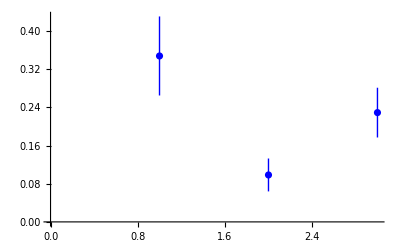

```mathematica
ListPlot[%133,PlotStyle->Blue]
```

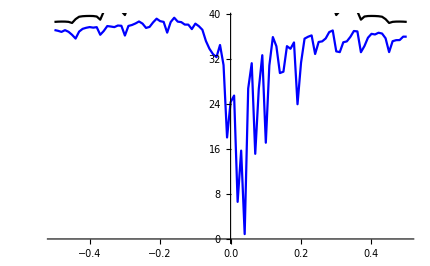

```mathematica
Show[ListLinePlot[Table[{ω,device2[ω,0.5,50]},{ω,Range[-0.5,0.5,0.01]}],PlotStyle->Blue,PlotRange->All],ListLinePlot[Table[{ω,device2[ω,0,50]},{ω,Range[-0.5,0.5,0.01]}],PlotStyle->Black,PlotRange->All]]
```

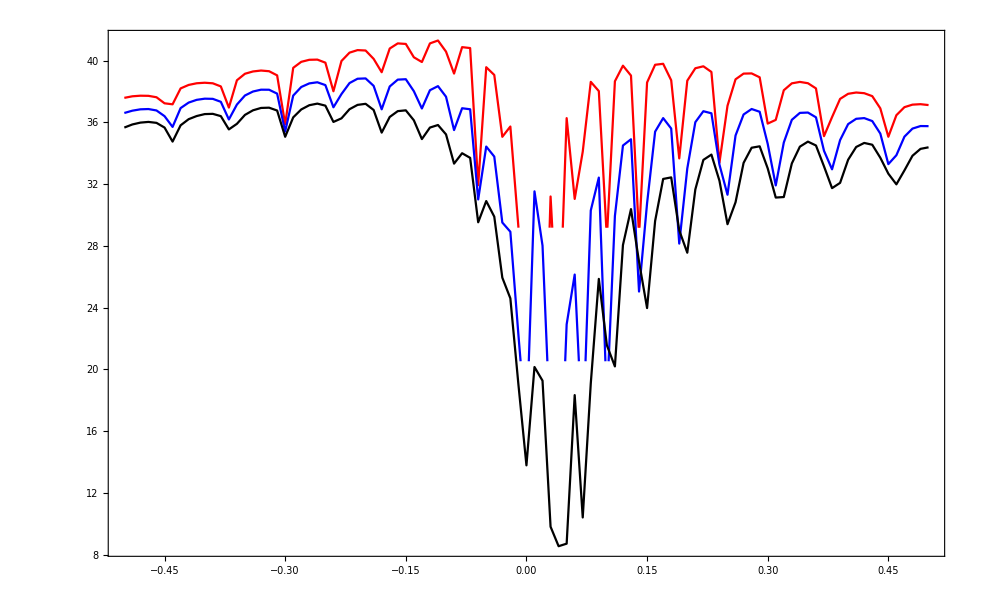

```mathematica
Show[ListLinePlot[%117,PlotStyle->Red],ListLinePlot[%122,PlotStyle->Blue],ListLinePlot[%123,PlotStyle->Black],PlotRange->All,Frame->True]
```

```mathematica
devicenew[ω_,ϵ1_,m_]:=Module[{Tin=T[1,m],list,b2},
list={{unitcell2[ω,0.0001,1,0,ϵ1,1],unitcell2[ω,0.0001,1,0,ϵ1,2],unitcell2[ω,0.0001,1,0,ϵ1,3],unitcell2[ω,0.0001,1,0,ϵ1,4],unitcell2[ω,0.0001,1,0,ϵ1,5],unitcell2[ω,0.0001,1,0,ϵ1,6],unitcell2[ω,0.0001,1,0,ϵ1,7],unitcell2[ω,0.0001,1,0,ϵ1,8],unitcell2[ω,0.0001,1,0,ϵ1,9],unitcell2[ω,0.0001,1,0,ϵ1,10],unitcell2[ω,0.0001,1,0,ϵ1,11],unitcell2[ω,0.0001,1,0,ϵ1,12],unitcell2[ω,0.0001,1,0,ϵ1,13],unitcell2[ω,0.0001,1,0,ϵ1,14],unitcell2[ω,0.0001,1,0,ϵ1,15],unitcell2[ω,0.0001,1,0,ϵ1,16],unitcell2[ω,0.0001,1,0,ϵ1,17],unitcell2[ω,0.0001,1,0,ϵ1,18],unitcell2[ω,0.0001,1,0,ϵ1,19],unitcell2[ω,0.0001,1,0,ϵ1,20],unitcell2[ω,0.0001,1,0,ϵ1,21],unitcell2[ω,0.0001,1,0,ϵ1,22],unitcell2[ω,0.0001,1,0,ϵ1,23],unitcell2[ω,0.0001,1,0,ϵ1,24],unitcell2[ω,0.0001,1,0,ϵ1,25],unitcell2[ω,0.0001,1,0,ϵ1,26],unitcell2[ω,0.0001,1,0,ϵ1,27],unitcell2[ω,0.0001,1,0,ϵ1,28],unitcell2[ω,0.0001,1,0,ϵ1,29],unitcell2[ω,0.0001,1,0,ϵ1,30],unitcell2[ω,0.0001,1,0,ϵ1,31],unitcell2[ω,0.0001,1,0,ϵ1,32],unitcell2[ω,0.0001,1,0,ϵ1,33],unitcell2[ω,0.0001,1,0,ϵ1,34],unitcell2[ω,0.0001,1,0,ϵ1,35],unitcell2[ω,0.0001,1,0,ϵ1,36],unitcell2[ω,0.0001,1,0,ϵ1,37],unitcell2[ω,0.0001,1,0,ϵ1,38],unitcell2[ω,0.0001,1,0,ϵ1,39],unitcell2[ω,0.0001,1,0,ϵ1,40],unitcell2[ω,0.0001,1,0,ϵ1,41],unitcell2[ω,0.0001,1,0,ϵ1,42],unitcell2[ω,0.0001,1,0,ϵ1,43],unitcell2[ω,0.0001,1,0,ϵ1,44],unitcell2[ω,0.0001,1,0,ϵ1,45],unitcell2[ω,0.0001,1,0,ϵ1,46],unitcell2[ω,0.0001,1,0,ϵ1,47],unitcell2[ω,0.0001,1,0,ϵ1,48],unitcell2[ω,0.0001,1,0,ϵ1,49],unitcell2[ω,0.0001,1,0,ϵ1,50]}};
sl1= Module[{J=SL[ω,0.0001,1,0,m]},Do[J=Inverse[IdentityMatrix[m]-list[[1,ζ]].ConjugateTranspose[Tin].J.Tin].list[[1,ζ]],{ζ,1,50}];
 J=J];
Il1:=Inverse[IdentityMatrix[m]-sl1.Tin.SL[ω,0.0001,1,0,m].Tin].sl1;
Ir1:=Inverse[IdentityMatrix[m]-SL[ω,0.0001,1,0,m].Tin.sl1.Tin].SL[ω,0.0001,1,0,m];gdd1:=Il1-ConjugateTranspose[Il1];grr1:=Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SL[ω,0.0001,1,0,m].Tin.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.Tin.grr1.Tin-Tin.GNON1.Tin.GNON1]]>tr[ω,0.0001,1,0,m],tr[ω,0.0001,1,0,m],Abs[Tr[gdd1.Tin.grr1.Tin-Tin.GNON1.Tin.GNON1]]]]
```

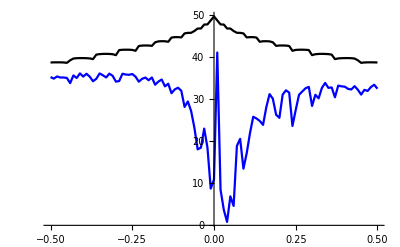

```mathematica
Show[ListLinePlot[Table[{ω,devicenew[ω,0.5,50]},{ω,Range[-0.5,0.5,0.01]}],PlotStyle->Blue,PlotRange->All],ListLinePlot[Table[{ω,devicenew[ω,0,50]},{ω,Range[-0.5,0.5,0.01]}],PlotStyle->Black,PlotRange->All],PlotRange->All]
```